```mathematica
(*间隔时间喝酒*)
```

```mathematica
f0[x_]:=
Module[{},If[x<0,0,98.71881069464635 ⅇ^(-0.29547136194732126 x) x^0.46815696152320363]];
f1[xV_,xN_,xT_,t_]:=Module[{vv=xV/xN,TT=xT/(xN-1)},
Sum[vv*f0[t-i*TT],{i,0,xN-1}]];
```

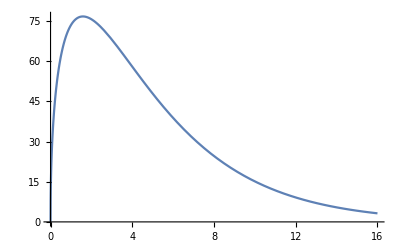

```mathematica
exp=98.71881069464635 ⅇ^(-0.29547136194732126 x) x^0.46815696152320363;
GG1=Plot[exp,{x,0,16}]
```

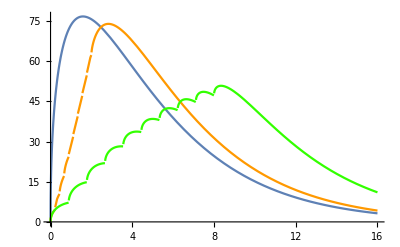

```mathematica
GG2=Plot[f1[1,10,2,x],{x,0,16},PlotStyle->Hue[0.1]];
GG3=Plot[f1[1,10,8,x],{x,0,16},PlotStyle->Hue[0.3]];
Show[GG1,GG2,GG3]
```

```mathematica
(*打点滴式的均匀饮入*)
```

```mathematica
f2=[xV_,xT_,t_]:=Module[{vv=xV/xT},Integrate[vv*f0[t-i],{i,0,xT}]]
```

```mathematica
Timing[GG3=Plot[f2[1,8,x],(x,0,16),PlotStyle->Hue[0.5]]]
Show[GG2]
Show[GG3,GG2,GG1]
```